```mathematica
.00EDO01=x''[t]+0.4x'[t]+9.04x[t]== 6 Exp[-t/5]Cos[3 t]
```

```mathematica
paso1=LaplaceTransform[EDO01,t,s]
```

EDO01/s

```mathematica
paso2=paso1/.{x[0]->0,x'[0]->0}
```

EDO01/s

```mathematica
paso3=Solve[paso2,LaplaceTransform[x[t],t,s]]
```

Solve::naqs: EDO01/s is not a quantified system of equations and inequalities.

Solve[EDO01/s,LaplaceTransform[x[t],t,s]]

```mathematica
sol=Simplify[InverseLaplaceTransform[(6 (0.2+s))/((9.04+0.4s+s^2)(9+(0.2+s)^2)),s,t]]//Expand
```

(0.+0.5 ⅈ) ⅇ^((-0.2-3. ⅈ) t) t-(0.+0.5 ⅈ) ⅇ^((-0.2+3. ⅈ) t) t

```mathematica
curva=t* Exp[-t/5]
```

ⅇ^(-t/5) t

```mathematica
derivada=D[curva,t]
```

ⅇ^(-t/5)-1/5 ⅇ^(-t/5) t

```mathematica
derivada2 = D[curva,{t,2}]
```

-2/5 ⅇ^(-t/5)+1/25 ⅇ^(-t/5) t

```mathematica
derivada2/.t->5
```

-1/(5 ⅇ)

```mathematica
Solve[derivada==0,t]
```

{{t→5}}

```mathematica
Maximize[{curva,(t≥0)&&(t≤30)},t]
```

{5/ⅇ,{t→5}}

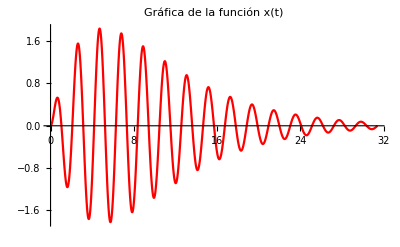

```mathematica
Plot[sol,{t,0,10 Pi},PlotLabel->"Gráfica de la función x(t)", LabelStyle->Directive[FontSize->12],PlotStyle->{Red}]
```

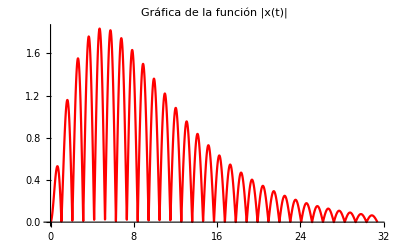

```mathematica
Plot[Abs[sol],{t,0,10 Pi},PlotLabel->"Gráfica de la función |x(t)|", LabelStyle->Directive[FontSize->12],PlotStyle->{Red}]
```

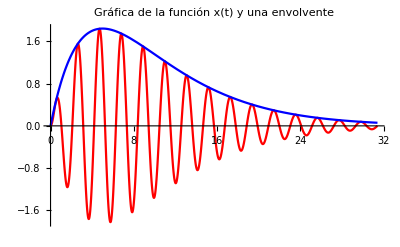

```mathematica
Plot[{sol, curva},{t,0,10 Pi},PlotLabel->"Gráfica de la función x(t) y una envolvente", LabelStyle->Directive[FontSize->12],PlotStyle->{Red, Blue}]
```

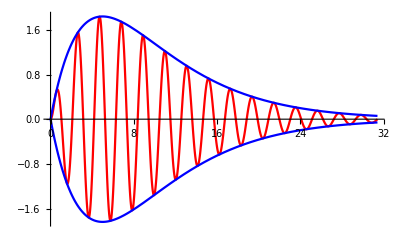

```mathematica
Plot[{sol,curva, -curva},{t,0,10 Pi},PlotStyle->{{Red,Dashing[None]},{Blue,Dashing[None]}, {Blue,Dashing[None]}}]
```